```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jogh/Dropbox/SIDIS (1)/paper/code

functions

```mathematica
xn[xbj_,Q_,Mp_]:= 2.0xbj/(1.0+Sqrt[1.0+4.0xbj^2 Mp^2/Q^2])

zn[xbj_,Q_,zh_,Mp_,MB_,PT_]:= xn[xbj,Q,Mp] zh/2.0/xbj(1.0+Sqrt[1.0- 4.0xbj^2 Mp^2(MB^2+PT^2)/Q^4/zh^2])
```

plot functions

```mathematica
color1=Function[{x},ColorData["AvocadoColors"][(x-0.94)/0.06*0.7]];
color2=Function[{x},ColorData["PlumColors"][(x-0.4)/0.6*0.72]];
```

```mathematica
legend[title_]:=Placed[BarLegend[Automatic,LegendMarkerSize->0.93*SIZE[[1]],LegendLabel->Style[title,12,Bold,FontFamily->"Helvetica"],LegendMargins->{{26, 0}, {0, 0}}],Top]

legend2[title_]:=BarLegend[{COLOR,RANGE[[3]]},CONTOURS,LegendMarkerSize->0.78*SIZE[[2]],LegendLabel->Style[title,10,FontFamily->"Helvetica"],LegendMargins->{{0, 0}, {10, 0}}]
COLOR=color1;

Clear[labelfunction]
labelfunction[id_,vars_,vals_,units_]:=Module[
{label=id<>"   ",table,it,format},

table=Table[(StringForm[(vars[[i]])<>"=`` ``  ",(vals[[i]]//ToString ),(units[[i]]//ToString )])//ToString,{i,1,vars//Length}];
For[it=1,it≤(vals//Length),it++,label=label <>table[[it]]];

format={"xbj"->"x_Bj","zh"->"z_h","qT"->"q_T","MB"->"M_B"};
label= 
label//StringReplace[#,format]&//Style[#,FontFamily->"Helvetica",10,Black]&
]

labelfunction2[vars_,vals_,units_]:=Module[
{label="",table,it,format},

table=Table[(StringForm[(vars[[i]])<>"=`` ``  ",(vals[[i]]//ToString ),(units[[i]]//ToString )])//ToString,{i,1,vars//Length}];
For[it=1,it≤(vals//Length),it++,label=label <>table[[it]]];

format={"xbj"->"x_Bj","zh"->"z_h","qT"->"q_T","MB"->"M_B"};
label= 
label//StringReplace[#,format]&//Style[#,FontFamily->"Helvetica",10,Black]&
]
```

```mathematica
xnplot2[region_,label1_,label2_]:=ContourPlot[
xn[xbj,Q,0.938]/xbj,{xbj,Q}∈region,
PlotRange->RANGE,
ColorFunction->COLOR,
Contours-> CONTOURS,
FrameLabel->FRAMELABEL,
LabelStyle->STYLE,
ColorFunctionScaling->COLORSCALING,
PlotLegends->LEGEND,
PlotLabel->label2,
AspectRatio->ASPECT,
ImagePadding->PAD,
ImageMargins->MARGIN,
ImageSize->SIZE,
ScalingFunctions->{"Linear","Log"},
Epilog->EPILOG[label1]
]

Clear[znplot3]
znplot3[region_,kin_,label_]:=Module[
{znfunction,regionplot,labelkin},
znfunction[zhin_,PTscaledin_]=(zn[xbj,Q,zhin,Mp,MB,Q PTscaledin]/zhin)/.kin;
regionplot=region/.kin;
labelkin=labelfunction["",{"Q","xbj"},{Q,xbj}/.kin,{"GeV",""}];
ContourPlot[znfunction[zh,PTscaled],{zh,PTscaled}∈(regionplot),
PlotRange->RANGE,
ColorFunction->COLOR,
Contours-> CONTOURS,
FrameLabel->FRAMELABEL,
ColorFunctionScaling->COLORSCALING,
PlotLegends->LEGEND,
PlotLabel->Style[label,10,Black,"Helvetica"],
LabelStyle->STYLE,
AspectRatio->ASPECT,
ImagePadding->PAD,
ImageMargins->MARGIN,
ImageSize->SIZE,
Epilog->EPILOG[labelkin]
]
]
```

regions

```mathematica
ℛjl=ImplicitRegion[0.15<(0.04442075337597726 Q^2)/xbj<0.83&&0.8798439999999998+((1.-xbj) Q^2)/xbj>3.8&&0.08≤xbj≤0.64&&1≤Q≤3.5,{xbj,Q}];
ℛherm=ImplicitRegion[0.1<(0.01931337103303359 Q^2)/xbj<0.85&&0.8798439999999998+((1.-xbj) Q^2)/xbj>10.&&0.023≤xbj≤0.6&&1≤Q≤5.5,{xbj,Q}];
ℛcomp=ImplicitRegion[0.1<(0.0033315565031982945 Q^2)/xbj<0.9&&0.8798439999999998+((1.-xbj) Q^2)/xbj>25.&&0.003≤xbj≤0.4&&1≤Q≤11,{xbj,Q}];

ℛjllog=ImplicitRegion[0.15<(0.04442075337597726Exp[2 Q])/xbj<0.83&&0.8798439999999998+((1.-xbj) Exp[2 Q])/xbj>3.8&&0.08≤xbj≤0.64&&Log[1]≤Q≤Log[3.5],{xbj,Q}];
ℛhermlog=ImplicitRegion[0.1<(0.01931337103303359 Exp[2 Q])/xbj<0.85&&0.8798439999999998+((1.-xbj) Exp[2 Q])/xbj>10.&&0.023≤xbj≤0.6&&Log[1]≤Q≤Log[5.5],{xbj,Q}];
ℛcomplog=ImplicitRegion[0.1<(0.0033315565031982945 Exp[2 Q])/xbj<0.9&&0.8798439999999998+((1.-xbj) Exp[2 Q])/xbj>25.&&0.003≤xbj≤0.4&&Log[1]≤Q≤Log[11],{xbj,Q}];



Clear[ℛzPT,ℛzPT2,PTMAX,PTMAX2]
PTMAX=1/(8 M^4 Q^2 xbj^2)(Q^2+2 M^2 xbj^2+Q √(Q^2+4 M^2 xbj^2)) √(-1/xbj^4(MB^2 Q^4 (Q-√(Q^2+4 M^2 xbj^2))^4+Q^4 (Q-√(Q^2+4 M^2 xbj^2))^2 (Q^2+2 M^2 xbj-Q √(Q^2+4 M^2 xbj^2))^2+2 M^2 Q^4 xbj^2 (Q^2+2 M^2 xbj-Q √(Q^2+4 M^2 xbj^2)) (2 M^2 xbj-Q (Q-√(Q^2+4 M^2 xbj^2)) (-1+zh))-2 M^2 Q^4 xbj^2 (Q^2+2 M^2 xbj-Q √(Q^2+4 M^2 xbj^2)) √(5+(2 Q (Q-√(Q^2+4 M^2 xbj^2)))/(M^2 xbj^2)) (2 M^2 xbj-Q (Q-√(Q^2+4 M^2 xbj^2)) (-1+zh))))/.xbj->xbj/.M->Mp;

PTMAX2=(√(-4 MB^2 Mp^2 xbj^2+Q^4 zh^2))/(2 Mp xbj);
ℛzPT=ImplicitRegion[{PT≤PTMAX,PT≤PTMAX2},{{zh,0.1,0.8},{PT,0.0,10}}];
ℛzPT2=ImplicitRegion[{PTscaled≤(PTMAX/Q),PTscaled≤(PTMAX2/Q)},{{zh,0.1,0.8},{PTscaled,0.0,10}}];
```

xN/xbj

## Settings

```mathematica
RANGE={{0.0,0.66},{1,15.0},{0.94,1.0}};
COLOR=color1;
CONTOURS={0.96,0.97,0.98,0.99,1.0};
ASPECT=0.85;
FRAMELABEL={"x_Bj","Q (GeV)"};
STYLE={10,FontFamily->"Helvetica",Black};
COLORSCALING=False;
LEGEND=False;
PAD={{40,0},{30,4}};
MARGIN={{0,0},{0,0}};
SIZE={72*8/3,72*8/3 ASPECT};
EPILOG=Inset[#,Scaled[{0.25,0.85}]]&;
```

## plots

```mathematica
jlabxnplot=xnplot2[ℛjllog,"",Style[" JLab  ",Black,10]];
hermesxnplot=xnplot2[ℛhermlog,"",Style[" HERMES ",Black,10,"Helvetica"]];
compassxnplot=xnplot2[ℛcomplog,"",Style[" COMPASS",Black,10,"Helvetica"]];
legendxn=legend2["x_N/x_Bj"];
```

zN/zh

## Settings

```mathematica
color3[0.5]
```

Hue[0.72, 0.9166666666666667, 0.5833333333333333]

```mathematica
Hue
```

```mathematica
FRAMELABEL={"z_h","P_(B, T) / Q"};
RANGE={{0,0.9},{0,1.7},{0.55,1.0}};
LEGEND=False;
STYLE={10,FontFamily->"Helvetica",Black};
CONTOURS={0.8,0.85,0.9,0.95,1.0};
CONTOURS={0.8,0.85,0.9,0.95,1.0};
COLORSCALING=False;
color3=Hue[Rescale[#,RANGE[[3]],{0.6,0.7}],Rescale[#,RANGE[[3]],{0.8,0.1}],Rescale[#,RANGE[[3]],{0.6,1.0}]]&;
COLOR=color3;
EPILOG=Inset[#,Scaled[{0.50,0.85}]]&;
PAD={{40,0},{30,0}};
```

## plots

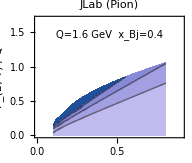

```mathematica
kinjl3={xbj->0.3,Q->Sqrt[2.5],MB->0.14,Mp->0.9383};
kincomp3={xbj->0.03,Q->Sqrt[5],MB->0.14,Mp->0.9383};
kinherm3={xbj->0.1,Q->Sqrt[4.0],MB->0.14,Mp->0.9383};

kinjl1={xbj->0.4,Q-> 1.6,MB->0.140,Mp->0.9383};
kinjl2={xbj->0.4,Q-> 1.6,MB->0.500,Mp->0.9383};
jlabznpionplot=znplot3[ℛzPT2,kinjl1,"JLab (Pion)"]
jlabznkaonplot=znplot3[ℛzPT2,kinjl2,"JLab (Kaon)"];


kinherm1={xbj->0.4,Q-> 2.5,MB->0.140,Mp->0.9383};
kinherm2={xbj->0.4,Q-> 2.5,MB->0.500,Mp->0.9383};
hermesznpionplot=znplot3[ℛzPT2,kinherm1,"HERMES (Pion)"];
hermesznkaonplot=znplot3[ℛzPT2,kinherm2,"HERMES (Kaon)"];


kincomp1={xbj->0.3,Q-> 3.0,MB->0.140,Mp->0.9383};
kincomp2={xbj->0.3,Q-> 3.0,MB->0.500,Mp->0.9383};
compassznpionplot=znplot3[ℛzPT2,kincomp1,"COMPASS (Pion)"];
compassznkaonplot=znplot3[ℛzPT2,kincomp2,"COMPASS (Kaon)"];

legendzn=legend2["z_N/z_h"];
```

Export figures

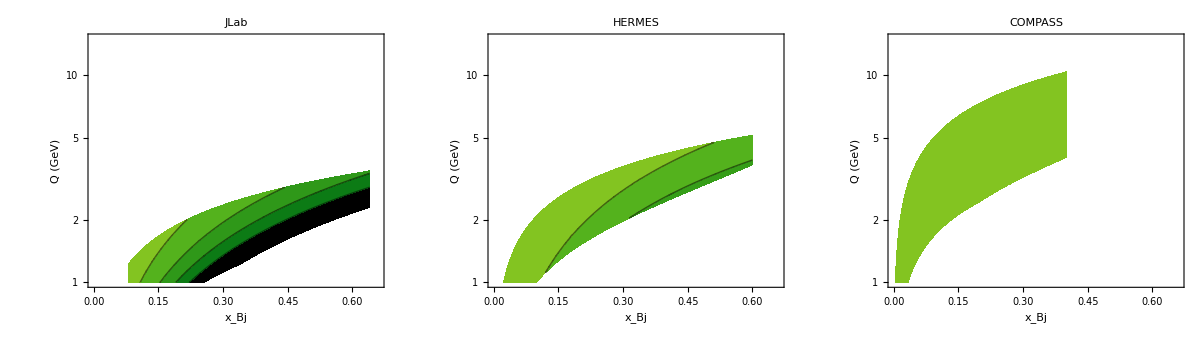

xnplots.pdf

```mathematica
GraphicsGrid[{{jlabxnplot,hermesxnplot,compassxnplot,legendxn}},
ImageSize-> { SIZE  3.8,1.5SIZE ASPECT },
Spacings->0,
Alignment->{{Right,Right,Right,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
Export["xnplots.pdf",%]
```

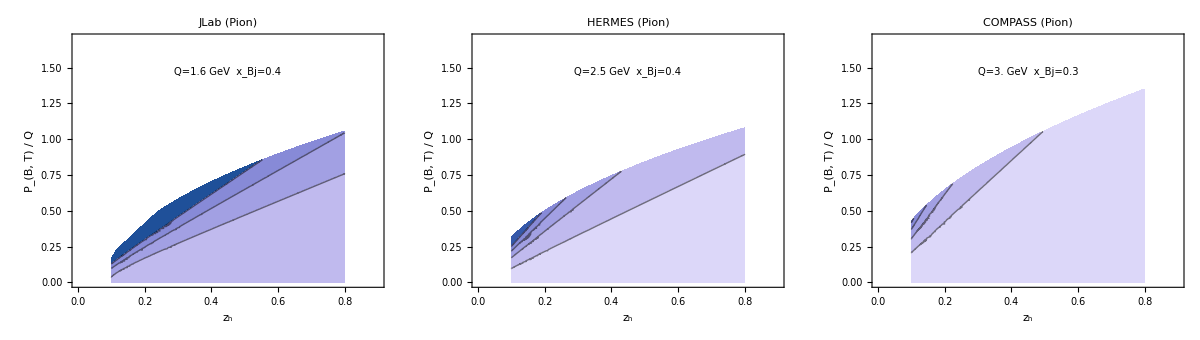

znpionplots.pdf

```mathematica
GraphicsGrid[{{jlabznpionplot,hermesznpionplot,compassznpionplot,legendzn}},
ImageSize-> { SIZE  3.8,1.5SIZE ASPECT },
Spacings->0,
Alignment->{{Right,Right,Right,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
Export["znpionplots.pdf",%]
```

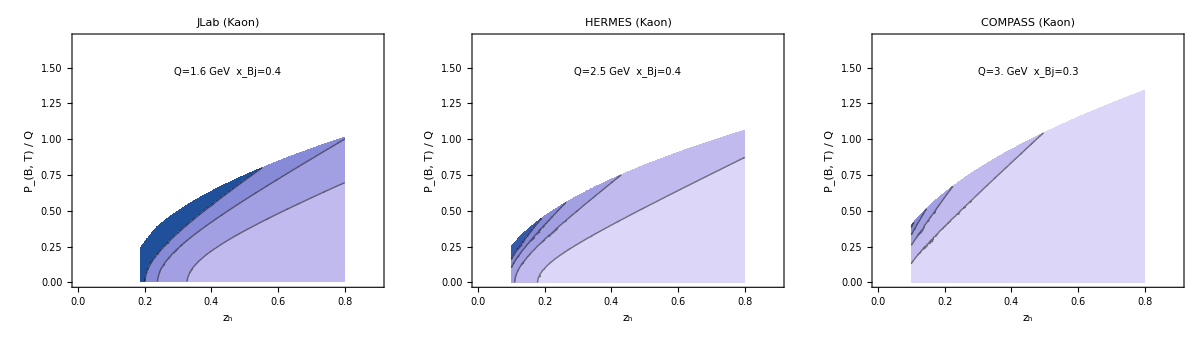

znkaonplots.pdf

```mathematica
GraphicsGrid[{{jlabznkaonplot,hermesznkaonplot,compassznkaonplot,legendzn}},
ImageSize-> { SIZE  3.8,1.5SIZE ASPECT },
Spacings->0,
Alignment->{{Right,Right,Right,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
Export["znkaonplots.pdf",%]
```

compare sizes

```mathematica
GraphicsGrid[{{jlabxnplot,hermesxnplot,compassxnplot,legendxn}},
ImageSize-> { SIZE  3.8,1.5SIZE ASPECT },
Spacings->0,
Alignment->{{Right,Right,Right,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
GraphicsGrid[{{jlabznpionplot,hermesznpionplot,compassznpionplot,legendzn}},
ImageSize-> { SIZE  3.8,1.5SIZE ASPECT },
Spacings->0,
Alignment->{{Right,Right,Right,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
```

-Graphics-

-Graphics-